# PRACTICAL 3 Plotting and Solving Third Order Solution Family Of ODE’s

```mathematica
Q.1   Solve and Plot y'''[x] - 6 y''[x] + 11 y'[x] - 6 y[x] ==0
with initial conditions y[0]==1 , y'[x]==2
y''[x]==3
```

```mathematica
sol1=DSolve[{y'''[x] - 6 y''[x] + 11 y'[x] - 6 y[x]==0,y[0]==1,y'[0]==2,y''[0]==3},y[x],x]
```

{{y[x]→-1/2 ⅇ^x (1-4 ⅇ^x+ⅇ^(2 x))}}

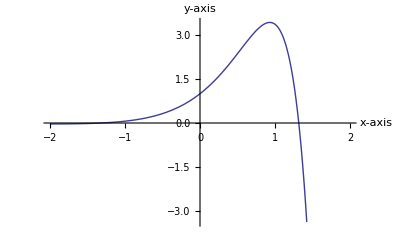

```mathematica
Plot[y[x]/.sol1,{x,-2,2},AxesLabel->{"x-axis","y-axis"}]
```

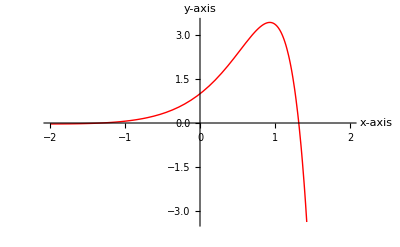

```mathematica
Plot[y[x]/.sol1,{x,-2,2},AxesLabel->{"x-axis","y-axis"},PlotStyle->Red]
```